```mathematica
l[n_]:=l0 b^(n)
Sll[1,k_]:=(1-m)/(1+m)
Srl[1,k_]:=2Sqrt[m]/(1+m)
Srr[1,k_]:=-(1-m)/(1+m)
Slr[1,k_]:=2Sqrt[m]/(1+m)
Sll[n_,k_]:=Sll[n-1,k]+(Exp[2I k l[n]]Srl[n-1,k]Sll[1,k]Slr[n-1,k])/(1-Exp[2I k l[n]]Srr[n-1,k]Sll[1,k])
Srl[n_,k_]:=Exp[I k l[n]]Srl[n-1,k]Srl[1,k]/(1-Exp[2I k l[n]]Sll[1,k]Srr[n-1,k])
Srr[n_,k_]:=Srr[1,k]+(Exp[2I k l[n]]Slr[1,k]Srr[n-1,k]Srl[1,k])/(1-Exp[2I k l[n]]Sll[1,k]Srr[n-1,k])
Slr[n_,k_]:=Exp[I k l[n]]Slr[1,k]Slr[n-1,k]/(1-Exp[2I k l[n]]Srr[n-1,k]Sll[1,k])
```

```mathematica
Manipulate[
Plot[Abs[Sll[n,k*Pi]/.{m->mm,l0->ll0,b->bb}]^2,{k,0,kmax},PlotRange->{0,1},AxesLabel->{"kπ","|R|^2"},GridLines->{{},{Abs[Sll[n,0]/.{m->mm,l0->ll0,b->bb}]^2}}],
{n,2,10,1,Appearance->"Labeled"},
{mm,2,20,1,Appearance->"Labeled"},
{{ll0,1},0,10,Appearance->"Labeled"},
{{bb,0.5},0,1,Appearance->"Labeled"},
{kmax,2,100,Appearance->"Labeled"}]
```

```mathematica
Sll[3,k]/.{b->1}//FullSimplify
Srr[3,k]/.{b->1}//FullSimplify
((1-m^n)/(1+m^n)+(1-m)/(1+m))/(1+(1-m^n)/(1+m^n)*(1-m)/(1+m))//FullSimplify
```

-(2 ⅇ^(2 ⅈ k l0) (-1+m) (1+m^2+(1+m)^2 Cos[2 k l0]))/((1+m) (2 ⅇ^(2 ⅈ k l0) (-1+m)^2+ⅇ^(4 ⅈ k l0) (-1+m)^2+(1+m)^2))

((-1+m) (1+m^2+(1+m)^2 Cos[2 k l0]))/((1+m) ((-1+m)^2+(1+m^2) Cos[2 k l0]-2 ⅈ m Sin[2 k l0]))

-1+2/(1+m^(1+n))

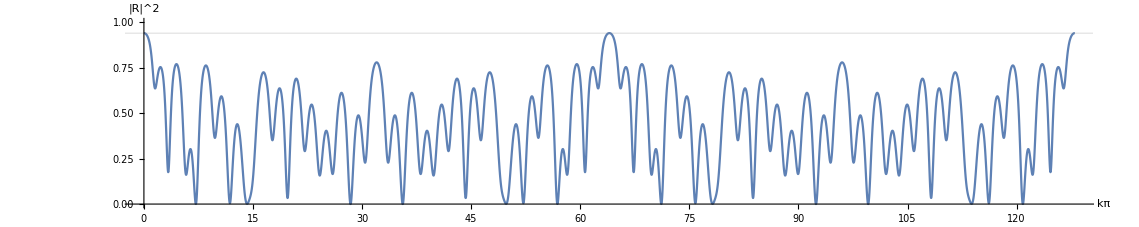

```mathematica
n=6;m=2;l0=1;b=0.5;
Plot[Abs[Sll[n,k Pi]]^2,{k,0,128},PlotRange->{0,1},AspectRatio->0.2,AxesLabel->{"kπ","|R|^2"},GridLines->{{},{Abs[Sll[n,0]]^2}},PlotPoints->100]
```

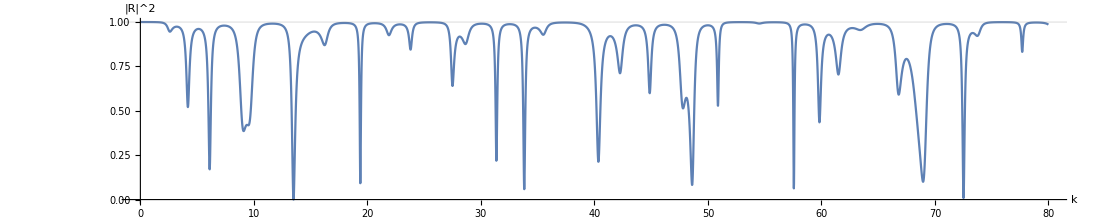

```mathematica
Abs[Sll[5,0]]^2//FullSimplify
```

Abs[(1-m^5)/(1+m^5)]^2

```mathematica
ClearAll[n,m,l0,b];
Sll[1,0]//FullSimplify
```

-1+2/(1+m)

```mathematica
m=2;l0=1;b=1/2;
NIntegrate[Abs[Sll[4,k]]^2,{k,0,2Pi},WorkingPrecision->20,MaxRecursion->20]/(2Pi)
```

0.29411764705882352961

```mathematica
Sll[4,k]
```

0

```mathematica
7/9//N
```

0.777778

```mathematica
Abs[(1-m)/(1+m)]
```

Abs[(1-m)/(1+m)]

```mathematica
ClearAll[m,l0,b];
Sll[2,k]//FullSimplify
```

-((1+ⅇ^(2 ⅈ b^2 k l0)) (-1+m^2))/(ⅇ^(2 ⅈ b^2 k l0) (-1+m)^2+(1+m)^2)

```mathematica
(1-m^2)/((-1+m)^2+(1+m)^2)//FullSimplify
```

-1/2+1/(1+m^2)

```mathematica
ClearAll[m,l0,b];
b=0.3;l0=1;
Manipulate[Plot[Abs[Sll[2,k]/.{m->mm}]^2,{k,0,100},PlotRange->{0,1}],{mm,2,10,1}]
```